```mathematica
SetDirectory[NotebookDirectory[]];
(files=FileNames["data/*.ods"])//TableForm
```

data\t1_t_in_ms_i_in_V_cu005.ods
data\t1_t_in_ms_i_in_V_cu01.ods
data\t1_t_in_ms_i_in_V_cu02.ods
data\t2_CP_tau0k4ms_t_in_ms_i_in_V_cu005.ods
data\t2_CP_tau0k5ms_t_in_ms_i_in_V_cu01.ods
data\t2_CP_tau0k5ms_t_in_ms_i_in_V_cu02.ods
data\t2_MG_tau0k3ms_t_in_ms_i_in_V_cu005.ods
data\t2_MG_tau0k5ms_t_in_ms_i_in_V_cu01.ods
data\t2_MG_tau0k5ms_t_in_ms_i_in_V_cu02.ods
data\t2_spinecho_t_in_ms_i_in_V_cu005.ods
data\t2_spinecho_t_in_ms_i_in_V_cu01.ods
data\t2_spinecho_t_in_ms_i_in_V_cu02.ods
data\t2stern_t_in_mus_i_in_v_cu02.ods
data\t2stern_t_in_mus_i_in_v_mineralol.ods

```mathematica
(t2stoel=First@Import["data/t2stern_t_in_mus_i_in_v_mineralol.ods"])//TableForm;
(t2stcu02=First@Import["data/t2stern_t_in_mus_i_in_v_cu02.ods"])//TableForm;
t1005=First@Import["data/t1_t_in_ms_i_in_V_cu005.ods"];
t101=First@Import["data/t1_t_in_ms_i_in_V_cu01.ods"];
t102=First@Import["data/t1_t_in_ms_i_in_V_cu02.ods"];
spin005=First@Import["data/t2_spinecho_t_in_ms_i_in_V_cu005.ods"];
spin01=First@Import["data/t2_spinecho_t_in_ms_i_in_V_cu01.ods"];
spin02=First@Import["data/t2_spinecho_t_in_ms_i_in_V_cu02.ods"];
mg005=First@Import["data/t2_MG_tau0k3ms_t_in_ms_i_in_V_cu005.ods"];
mg01=First@Import["data/t2_MG_tau0k5ms_t_in_ms_i_in_V_cu01.ods"];
mg02=First@Import["data/t2_MG_tau0k5ms_t_in_ms_i_in_V_cu02.ods"];
cp005=First@Import["data/t2_CP_tau0k4ms_t_in_ms_i_in_V_cu005.ods"];
cp01=First@Import["data/t2_CP_tau0k5ms_t_in_ms_i_in_V_cu01.ods"];
cp02=First@Import["data/t2_CP_tau0k5ms_t_in_ms_i_in_V_cu02.ods"];
```

```mathematica
ToErrorForm[{x1_,x2_}]:={(x1+x2)/2,Abs[x2-x1]/2};
<<"ErrorBarPlots`"
```

## T_2^*

{{0.370492,0.0478545},{448.429,28.1648},{0.086246,0.0485313}}

{{0.303188,0.0458959},{433.604,30.2053},{0.0610739,0.050498}}

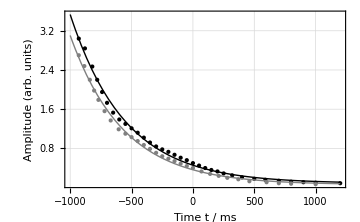

```mathematica
dats={t2stoel,t2stcu02};
fits=Module[{fit},
Print[ToErrorForm/@(fit=NonlinearModelFit[#1,a* E^(-x/b)+c,{{a,0.5},{b,500},{c,0}},x])["ParameterConfidenceIntervals"]];
fit
]&/@dats;
Show[
ListPlot[dats,PlotRange->All,PlotStyle->{Black,Gray}],
Plot[{Normal@fits⟦1⟧,Normal@fits⟦2⟧},{x,-1000,1200},PlotStyle->{Black,Gray}],
ImageSize->Medium,Frame->True,FrameLabel->{"Time t / ms","Amplitude (arb. units)"},Axes->None,GridLines->Automatic
]
```

## T_2

{{-3.99407,0.0435192},{20.4734,0.610638},{1.99772,0.0383346}}

{{-3.97584,0.0370221},{9.63981,0.247873},{1.95093,0.0304129}}

{{-5.26085,0.0474755},{4.24683,0.107315},{2.62475,0.042459}}

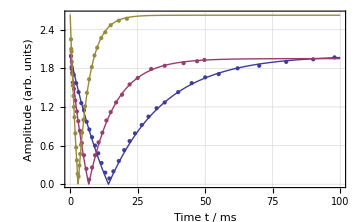

```mathematica
dats={t1005,t101,t102};
fits=Module[{fit},
Print[ToErrorForm/@(fit=NonlinearModelFit[#1,Abs[a* E^(-x/b)+c],{{a,-4},{b,7},{c,2}},x])["ParameterConfidenceIntervals"]];
fit
]&/@dats;
Show[
ListPlot[dats,PlotRange->All],
Plot[{Normal@fits⟦1⟧,Normal@fits⟦2⟧,Normal@fits⟦3⟧},{x,0,100}],
ImageSize->Medium,Frame->True,FrameLabel->{"Time t / ms","Amplitude (arb. units)"},Axes->None,GridLines->Automatic
]
```

## T_1 - Spin Echo

{{2.19272,0.0418653},{11.0051,0.567447},{-0.0965997,0.0488123}}

{{2.0958,0.0318941},{4.92422,0.23615},{0.0280683,0.0358801}}

{{2.76369,0.0277249},{2.20792,0.0690154},{0.0291403,0.0281363}}

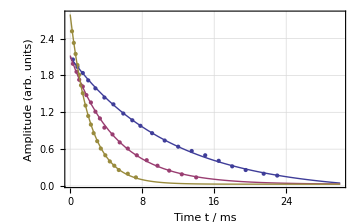

```mathematica
dats={spin005,spin01,spin02};
fits=Module[{fit},
Print[ToErrorForm/@(fit=NonlinearModelFit[#1,a* E^(-x/b)+c,{{a,2},{b,7},{c,0}},x])["ParameterConfidenceIntervals"]];
fit
]&/@dats;
Show[
ListPlot[dats,PlotRange->All],
Plot[{Normal@fits⟦1⟧,Normal@fits⟦2⟧,Normal@fits⟦3⟧},{x,0,30},PlotRange->All],
ImageSize->Medium,Frame->True,FrameLabel->{"Time t / ms","Amplitude (arb. units)"},Axes->None,GridLines->Automatic
]
```

## T_1 - MG

{{1.89398,0.0081887},{20.1747,0.266894},{0.0981004,0.0095061}}

{{2.08809,0.0289923},{10.1668,0.423914},{0.0112963,0.0335434}}

{{3.35498,0.0725658},{4.49674,0.195569},{0.0397695,0.027642}}

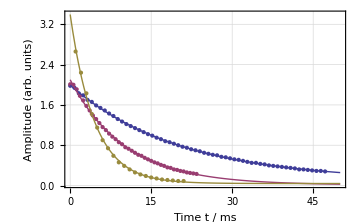

```mathematica
dats={mg005,mg01,mg02};
fits=Module[{fit},
Print[ToErrorForm/@(fit=NonlinearModelFit[#1,a* E^(-x/b)+c,{{a,2},{b,7},{c,0}},x])["ParameterConfidenceIntervals"]];
fit
]&/@dats;
Show[
ListPlot[dats,PlotRange->All],
Plot[{Normal@fits⟦1⟧,Normal@fits⟦2⟧,Normal@fits⟦3⟧},{x,0,50},PlotRange->All],
ImageSize->Medium,Frame->True,FrameLabel->{"Time t / ms","Amplitude (arb. units)"},Axes->None,GridLines->Automatic
]
```

## T_1 - CP

{{1.86295,0.103574},{8.78842,0.698269},{0.0316697,0.0548157},{7.67763,0.129181},{0.125548,0.0700434},{-4.0169×10^7,0.},{-0.323508,0.0429995}}

{{1.88691,0.253554},{5.87279,0.987763},{0.073612,0.0472455},{5.98507,0.12797},{0.0895698,0.145573},{17.403,119.862},{-0.286157,0.049176}}

{{5.27052,2.10329},{2.56408,0.610151},{0.0905354,0.0633983},{9.13469,1.12776},{-0.0808608,0.257628},{2.79166×10^6,0.},{-0.986385,0.248078}}

{0.999161,0.998966,0.999773}

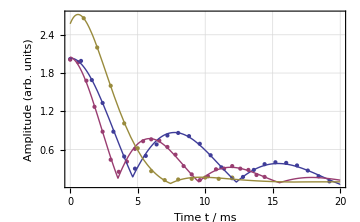

```mathematica
dats={cp005,cp01,cp02};
fits=Module[{fit},
Print[ToErrorForm/@(fit=NonlinearModelFit[#1,a* E^(-x/b)*(Abs[Cos[π x/d+g]]+e E^(-x/f))+c,{{a,2},{b,7},{c,0},{d,7},{e,0.2},{f,7},{g,0}},x])["ParameterConfidenceIntervals"]];
fit
]&/@dats;
#["RSquared"]&/@fits
Show[
ListPlot[dats,PlotRange->All],
Plot[{Normal@fits⟦1⟧,Normal@fits⟦2⟧,Normal@fits⟦3⟧},{x,0,20},PlotRange->{0,4}],
ImageSize->Medium,Frame->True,FrameLabel->{"Time t / ms","Amplitude (arb. units)"},Axes->None,GridLines->Automatic
]
```